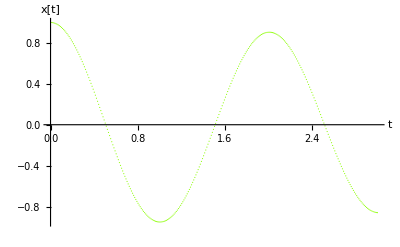

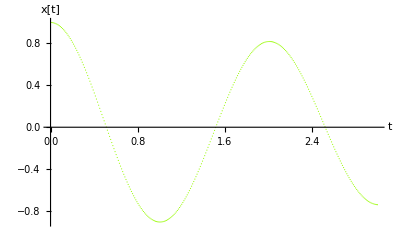

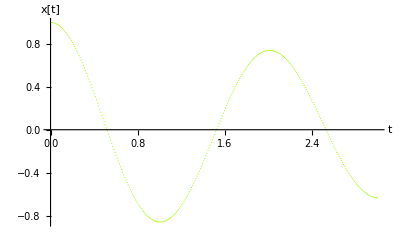

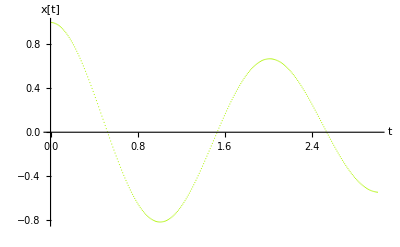

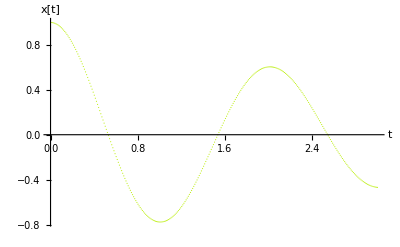

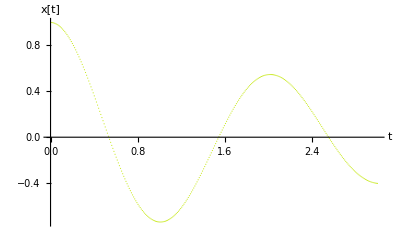

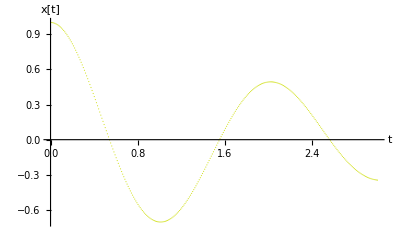

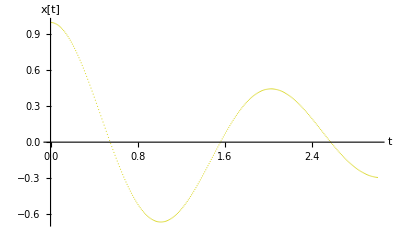

```mathematica
RK4ODE[G_,x0_,f0_,dx_,Ns_]:=Module[{k1,k2,k3,k4,retvals,index,xn,fn},retvals=Table[{0.0,0.0},{i,1,Ns}];
xn=x0;
fn=f0;
retvals⟦1⟧={x0,f0};
For[index=2,index≤Ns,index=index+1,
k1=dx G[xn,fn];
k2=dx G[xn+dx/2,fn+k1/2];
k3=dx G[xn+dx/2,fn+k2/2];
k4=dx G[xn+dx,fn+k3];
fn=fn+1/3 (k1/2+k2+k3+k4/2);
xn=xn+dx;
retvals⟦index⟧={xn,fn};
];
Return[retvals];
]
plots={};
m=2.;
k=19.6;
Nsteps=300;
dt=3.0/(Nsteps-1);
z=0;







For[
(*The size of the For Loop*)
d=.0,
d<10,
d+=.1;

G[x_,f_]:={f⟦2⟧,-(k/m) f⟦1⟧-d*f[[2]]};


fvals1=RK4ODE[G,0.0,{1,0},3.0/(Nsteps-1),Nsteps];
X=Table[{fvals1⟦j,1⟧,fvals1⟦j,2,1⟧},{j,1,Length[fvals1]}];

(*This Handles the Colored Graphs*)
z+=.1;
r=((Sin[z]+1)/2);
g=((Cos[z]+1)/2);
b=((-Cos[z]+1)/2);



(*Graphs the Points and Saves them to a List*)
xplot = ListPlot[
X,
AxesLabel->{"t","x[t]"},
PlotStyle->{
PointSize[0.002],
RGBColor[r,g,b]
}];
AppendTo[plots,xplot];
Print[xplot];
]
Show[plots,PlotRange->{{0,3},{-1.1,1.1}}]
```